```mathematica
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));

ϕdet[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

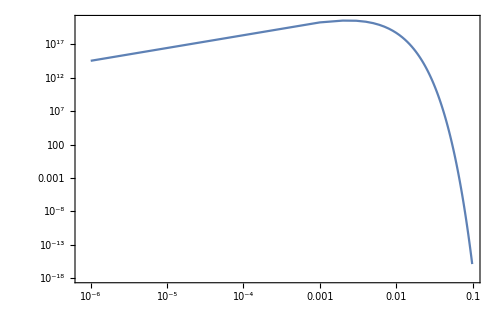

```mathematica
p0=ListLogLogPlot[Table[{x,ϕdet[10^16,0,x]},{x,10^-6,10^-1,0.001}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

```mathematica
SetDirectory[NotebookDirectory[]];
greybodydata=Import["interpolation.dat","Table"];
```

```mathematica
func=Interpolation[greybodydata];
```

```mathematica
f[x_]:=func[x];
```

```mathematica
ϕdetinterpol[mpbh_?NumericQ,x_?NumericQ]:=1/(2*π)*(27*x^2*f[x])/(Exp[8*π*x]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

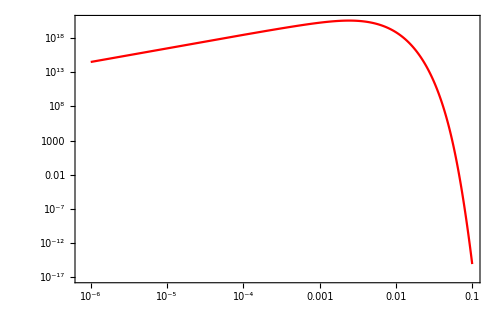

```mathematica
pin0=ListLogLogPlot[Table[{x/(G*10^16*5.62*10^23),ϕdetinterpol[10^16,x]},{x,G*10^16*5.62*10^23*10^-6,G*10^16*5.62*10^23*10^-1,G*10^16*5.62*10^23*0.0001}],Joined->True,Frame->True,PlotStyle->Red,ImageSize->500]//Quiet
```

```mathematica
data={{0.0001,3.18941*10^18},{0.000102329,3.33752*10^18},{0.000104713,3.49244*10^18},{0.000107152,3.65449*10^18},{0.000109648,3.82399*10^18},{0.000112202,4.00128*10^18},{0.000114815,4.18671*10^18},{0.00011749,4.38065*10^18},{0.000120226,4.58349*10^18},{0.000123027,4.79561*10^18},{0.000125893,5.01745*10^18},{0.000128825,5.24943*10^18},{0.000131826,5.49202*10^18},{0.000134896,5.74569*10^18},{0.000138038,6.01093*10^18},{0.000141254,6.28827*10^18},{0.000144544,6.57824*10^18},{0.000147911,6.8814*10^18},{0.000151356,7.19835*10^18},{0.000154882,7.52969*10^18},{0.000158489,7.87606*10^18},{0.000162181,8.23813*10^18},{0.000165959,8.61659*10^18},{0.000169824,9.01217*10^18},{0.00017378,9.42561*10^18},{0.000177828,9.8577*10^18},{0.00018197,1.03093*10^19},{0.000186209,1.07811*10^19},{0.000190546,1.12742*10^19},{0.000194984,1.17894*10^19},{0.000199526,1.23277*10^19},{0.000204174,1.28901*10^19},{0.00020893,1.34775*10^19},{0.000213796,1.40912*10^19},{0.000218776,1.47323*10^19},{0.000223872,1.54018*10^19},{0.000229087,1.6101*10^19},{0.000234423,1.68312*10^19},{0.000239883,1.75937*10^19},{0.000245471,1.83898*10^19},{0.000251189,1.9221*10^19},{0.00025704,2.00887*10^19},{0.000263027,2.09944*10^19},{0.000269153,2.19398*10^19},{0.000275423,2.29265*10^19},{0.000281838,2.39561*10^19},{0.000288403,2.50304*10^19},{0.000295121,2.61513*10^19},{0.000301995,2.73207*10^19},{0.00030903,2.85404*10^19},{0.000316228,2.98125*10^19},{0.000323594,3.11392*10^19},{0.000331131,3.25225*10^19},{0.000338844,3.39646*10^19},{0.000346737,3.5468*10^19},{0.000354813,3.7035*10^19},{0.000363078,3.86679*10^19},{0.000371535,4.03694*10^19},{0.000380189,4.2142*10^19},{0.000389045,4.39885*10^19},{0.000398107,4.59115*10^19},{0.00040738,4.79139*10^19},{0.000416869,4.99986*10^19},{0.00042658,5.21686*10^19},{0.000436516,5.44268*10^19},{0.000446684,5.67765*10^19},{0.000457088,5.92209*10^19},{0.000467735,6.17631*10^19},{0.00047863,6.44065*10^19},{0.000489779,6.71545*10^19},{0.000501187,7.00106*10^19},{0.000512861,7.29832*10^19},{0.000524807,7.61519*10^19},{0.000537032,7.9448*10^19},{0.000549541,8.2876*10^19},{0.000562341,8.64403*10^19},{0.00057544,9.01451*10^19},{0.000588844,9.39949*10^19},{0.00060256,9.79943*10^19},{0.000616595,1.02148*10^20},{0.000630957,1.0646*10^20},{0.000645654,1.10935*10^20},{0.000660693,1.15578*10^20},{0.000676083,1.20394*10^20},{0.000691831,1.25386*10^20},{0.000707946,1.3056*10^20},{0.000724436,1.35919*10^20},{0.00074131,1.41468*10^20},{0.000758578,1.47211*10^20},{0.000776247,1.53153*10^20},{0.000794328,1.59296*10^20},{0.000812831,1.65645*10^20},{0.000831764,1.72204*10^20},{0.000851138,1.78974*10^20},{0.000870964,1.85959*10^20},{0.000891251,1.93162*10^20},{0.000912011,2.00585*10^20},{0.000933254,2.08228*10^20},{0.000954993,2.16094*10^20},{0.000977237,2.24184*10^20},{0.001,2.32496*10^20},{0.00102329,2.41031*10^20},{0.00104713,2.49787*10^20},{0.00107152,2.58763*10^20},{0.00109648,2.67955*10^20},{0.00112202,2.7736*10^20},{0.00114815,2.87095*10^20},{0.0011749,2.97512*10^20},{0.00120226,3.08172*10^20},{0.00123027,3.19069*10^20},{0.00125893,3.30194*10^20},{0.00128825,3.4154*10^20},{0.00131826,3.53096*10^20},{0.00134896,3.64851*10^20},{0.00138038,3.76791*10^20},{0.00141254,3.88902*10^20},{0.00144544,4.01167*10^20},{0.00147911,4.13568*10^20},{0.00151356,4.26085*10^20},{0.00154882,4.38695*10^20},{0.00158489,4.51376*10^20},{0.00162181,4.64102*10^20},{0.00165959,4.76843*10^20},{0.00169824,4.89572*10^20},{0.0017378,5.04177*10^20},{0.00177828,5.18963*10^20},{0.0018197,5.33742*10^20},{0.00186209,5.48473*10^20},{0.00190546,5.63115*10^20},{0.00194984,5.77622*10^20},{0.00199526,5.91948*10^20},{0.00204174,6.06043*10^20},{0.0020893,6.19858*10^20},{0.00213796,6.33338*10^20},{0.00218776,6.4643*10^20},{0.00223872,6.60502*10^20},{0.00229087,6.76002*10^20},{0.00234423,6.91024*10^20},{0.00239883,7.05498*10^20},{0.00245471,7.19354*10^20},{0.00251189,7.32519*10^20},{0.0025704,7.44923*10^20},{0.00263027,7.56493*10^20},{0.00269153,7.68248*10^20},{0.00275423,7.81843*10^20},{0.00281838,7.94404*10^20},{0.00288403,8.05851*10^20},{0.00295121,8.16103*10^20},{0.00301995,8.25085*10^20},{0.0030903,8.32725*10^20},{0.00316228,8.42672*10^20},{0.00323594,8.56111*10^20},{0.00331131,8.67839*10^20},{0.00338844,8.77769*10^20},{0.00346737,8.85818*10^20},{0.00354813,8.91916*10^20},{0.00363078,8.96003*10^20},{0.00371535,9.05122*10^20},{0.00380189,9.11873*10^20},{0.00389045,9.16169*10^20},{0.00398107,9.18191*10^20},{0.0040738,9.19959*10^20},{0.00416869,9.19065*10^20},{0.0042658,9.15513*10^20},{0.00436516,9.09331*10^20},{0.00446684,9.01327*10^20},{0.00457088,8.90938*10^20},{0.00467735,8.78032*10^20},{0.0047863,8.67754*10^20},{0.00489779,8.61991*10^20},{0.00501187,8.52703*10^20},{0.00512861,8.3884*10^20},{0.00524807,8.22143*10^20},{0.00537032,8.03548*10^20},{0.00549541,7.86912*10^20},{0.00562341,7.67441*10^20},{0.0057544,7.50622*10^20},{0.00588844,7.31393*10^20},{0.0060256,7.09009*10^20},{0.00616595,6.84118*10^20},{0.00630957,6.56633*10^20},{0.00645654,6.27653*10^20},{0.00660693,6.01465*10^20},{0.00676083,5.70136*10^20},{0.00691831,5.38138*10^20},{0.00707946,5.04854*10^20},{0.00724436,4.70033*10^20},{0.0074131,4.34913*10^20},{0.00758578,3.9977*10^20},{0.00776247,3.66565*10^20},{0.00794328,3.3371*10^20},{0.00812831,3.01451*10^20},{0.00831764,2.68478*10^20},{0.00851138,2.37606*10^20},{0.00870964,2.08999*10^20},{0.00891251,1.82108*10^20},{0.00912011,1.57318*10^20},{0.00933254,1.34779*10^20},{0.00954993,1.14536*10^20},{0.00977237,9.66311*10^19},{0.01,8.08133*10^19},{0.0102329,6.6826*10^19},{0.0104713,5.49835*10^19},{0.0107152,4.47387*10^19},{0.0109648,3.61936*10^19},{0.0112202,2.91087*10^19},{0.0114815,2.32986*10^19},{0.011749,1.85093*10^19},{0.0120226,1.46472*10^19},{0.0123027,1.15481*10^19},{0.0125893,9.02122*10^18},{0.0128825,7.05542*10^18},{0.0131826,5.517*10^18},{0.0134896,4.28973*10^18},{0.0138038,3.33592*10^18},{0.0141254,2.60052*10^18},{0.0144544,2.02679*10^18},{0.0147911,1.57221*10^18},{0.0151356,1.22329*10^18},{0.0154882,9.43226*10^17},{0.0158489,7.23533*10^17},{0.0162181,5.5158*10^17},{0.0165959,4.15512*10^17},{0.0169824,3.07462*10^17},{0.017378,2.2475*10^17},{0.0177828,1.60939*10^17},{0.018197,1.13536*10^17},{0.0186209,7.89337*10^16},{0.0190546,5.39144*10^16},{0.0194984,3.64196*10^16},{0.0199526,2.42928*10^16},{0.0204174,1.60065*10^16},{0.020893,1.04639*10^16},{0.0213796,6.8101*10^15},{0.0218776,4.42359*10^15},{0.0223872,2.86997*10^15},{0.0229087,1.86294*10^15},{0.0234423,1.20432*10^15},{0.0239883,7.71942*10^14},{0.0245471,4.90822*10^14},{0.0251189,3.07664*10^14},{0.025704,1.89599*10^14},{0.0263027,1.15349*10^14},{0.0269153,6.9261*10^13},{0.0275423,4.10325*10^13},{0.0281838,2.3977*10^13},{0.0288403,1.3815*10^13},{0.0295121,7.84602*10^12},{0.0301995,4.39085*10^12},{0.030903,2.42045*10^12},{0.0316228,1.31384*10^12},{0.0323594,7.01983*10^11},{0.0331131,3.69055*10^11},{0.0338844,1.90841*10^11},{0.0346737,9.70287*10^10},{0.0354813,4.84847*10^10},{0.0363078,2.38018*10^10},{0.0371535,1.14746*10^10},{0.0380189,5.43002*10^9},{0.0389045,2.52124*10^9},{0.0398107,1.14811*10^9},{0.040738,5.12521*10^8},{0.0416869,2.24181*10^8},{0.042658,9.60364*10^7},{0.0436516,4.0273*10^7},{0.0446684,1.65241*10^7},{0.0457088,6.63015*10^6},{0.0467735,2.6002*10^6},{0.047863,996175.},{0.0489779,372626.},{0.0501187,136012.},{0.0512861,48417.4},{0.0524807,16799.3},{0.0537032,5677.84},{0.0549541,1868.17},{0.0562341,598.022},{0.057544,186.126},{0.0588844,56.2864},{0.060256,16.5277},{0.0616595,4.70908},{0.0630957,1.30098},{0.0645654,0.348261},{0.0660693,0.0902645},{0.0676083,0.022635},{0.0691831,0.00548736},{0.0707946,0.00128505},{0.0724436,0.000290472},{0.074131,0.0000633221},{0.0758578,0.0000133017},{0.0776247,2.69018*10^-6},{0.0794328,5.23358*10^-7},{0.0812831,9.78509*10^-8},{0.0831764,1.75662*10^-8},{0.0851138,3.02499*10^-9},{0.0870964,4.99213*10^-10},{0.0891251,7.88733*10^-11},{0.0912011,1.19184*10^-11},{0.0933254,1.72066*10^-12},{0.0954993,2.37085*10^-13},{0.0977237,3.11437*10^-14},{0.1,3.89592*10^-15},{0.102329,4.63586*10^-16},{0.104713,5.24112*10^-17},{0.107152,5.62307*10^-18},{0.109648,5.71806*10^-19},{0.112202,5.50437*10^-20},{0.114815,5.00951*10^-21},{0.11749,4.30471*10^-22},{0.120226,3.48796*10^-23},{0.123027,2.66125*10^-24},{0.125893,1.90931*10^-25},{0.128825,1.28624*10^-26},{0.131826,8.12425*10^-28},{0.134896,4.80409*10^-29},{0.138038,2.65544*10^-30},{0.141254,1.36987*10^-31},{0.144544,6.58471*10^-33},{0.147911,2.9444*10^-34},{0.151356,1.22273*10^-35},{0.154882,4.70742*10^-37},{0.158489,1.67723*10^-38},{0.162181,5.52047*10^-40},{0.165959,1.67544*10^-41},{0.169824,4.67986*10^-43},{0.17378,1.20073*10^-44},{0.177828,2.8243*10^-46},{0.18197,6.07782*10^-48},{0.186209,1.19414*10^-49},{0.190546,2.13754*10^-51},{0.194984,3.47841*10^-53},{0.199526,5.13442*10^-55},{0.204174,6.85899*10^-57},{0.20893,8.27326*10^-59},{0.213796,8.98894*10^-61},{0.218776,8.77602*10^-63},{0.223872,7.68002*10^-65},{0.229087,6.00891*10^-67},{0.234423,4.19242*10^-69},{0.239883,2.60142*10^-71},{0.245471,1.43168*10^-73},{0.251189,6.96883*10^-76},{0.25704,2.99163*10^-78},{0.263027,1.12932*10^-80},{0.269153,3.73759*10^-83},{0.275423,1.08118*10^-85},{0.281838,2.72503*10^-88},{0.288403,5.96517*10^-91},{0.295121,1.13038*10^-93},{0.301995,1.84806*10^-96},{0.30903,2.59779*10^-99},{0.316228,3.12869*10^-102},{0.323594,3.21681*10^-105},{0.331131,2.81316*10^-108},{0.338844,2.08464*10^-111},{0.346737,1.30395*10^-114},{0.354813,6.85751*10^-118},{0.363078,3.01992*10^-121},{0.371535,1.10906*10^-124},{0.380189,3.38222*10^-128},{0.389045,8.52826*10^-132},{0.398107,1.77013*10^-135},{0.40738,3.01071*10^-139},{0.416869,4.17673*10^-143},{0.42658,4.70377*10^-147},{0.436516,4.27946*10^-151},{0.446684,3.12972*10^-155},{0.457088,1.83058*10^-159},{0.467735,8.51875*10^-164},{0.47863,3.1373*10^-168},{0.489779,9.09415*10^-173},{0.501187,2.06335*10^-177},{0.512861,3.6434*10^-182},{0.524807,4.97773*10^-187},{0.537032,5.23059*10^-192},{0.549541,4.20153*10^-197},{0.562341,2.56382*10^-202},{0.57544,1.18088*10^-207},{0.588844,4.07869*10^-213},{0.60256,1.04935*10^-218},{0.616595,1.99719*10^-224},{0.630957,2.79239*10^-230},{0.645654,2.84752*10^-236},{0.660693,2.10233*10^-242},{0.676083,1.11534*10^-248},{0.691831,4.21938*10^-255},{0.707946,1.12928*10^-261},{0.724436,2.1211*10^-268},{0.74131,2.773*10^-275},{0.758578,2.50208*10^-282},{0.776247,1.54477*10^-289},{0.794328,6.46842*10^-297},{0.812831,1.82045*10^-304},{0.831764,3.411794699652491*10^-312},{0.851138,4.217942333481099*10^-320},{0.870964,3.406607768616595*10^-328},{0.891251,1.779674465418530*10^-336},{0.912011,5.953177417997794*10^-345},{0.933254,1.261935402960843*10^-353},{0.954993,1.677222355364515*10^-362},{0.977237,1.382569792357324*10^-371},{1.,6.990272021502518*10^-381}};//Quiet
```

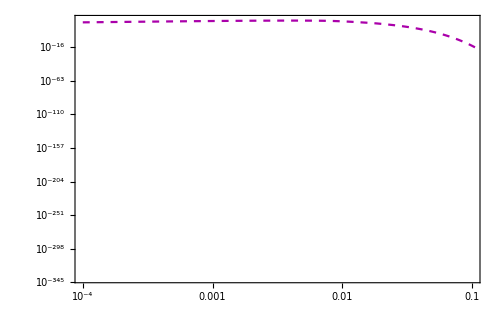

```mathematica
r0=ListLogLogPlot[Table[{data[[i,1]],data[[i,2]]},{i,Length[data]}],PlotRange->{{10^-4,10^-1},Automatic},PlotStyle->{Darker[Magenta],Dashed},Frame->True,Joined->True,ImageSize->500]
```

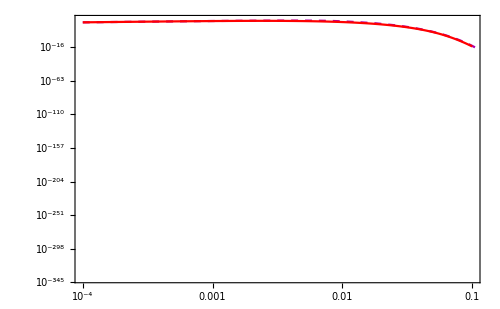

```mathematica
Show[r0,pin0]
```

```mathematica
data1=Import["instantaneous_primary_spectra16.txt","Table"];
```

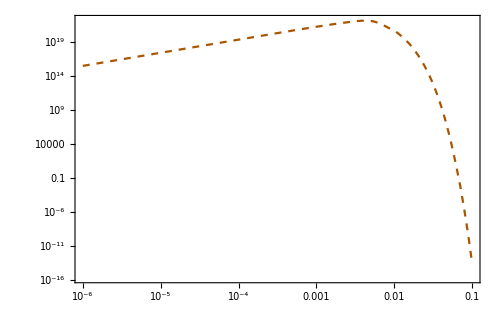

```mathematica
q0=ListLogLogPlot[Table[{data1[[i,1]],data1[[i,7]]},{i,Length[data1]}],PlotRange->{{10^-6,10^-1},Automatic},PlotStyle->{Darker[Orange],Dashed},Frame->True,Joined->True,ImageSize->500]
```

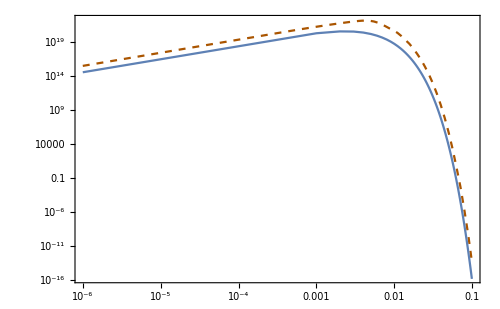

```mathematica
Show[q0,p0]
```

```mathematica
(**********************************************************************************************************************************************)
```

```mathematica
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));

ϕdet[mpbh_?NumericQ,astar_?NumericQ,e_?NumericQ]:=1/(2*π)*(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

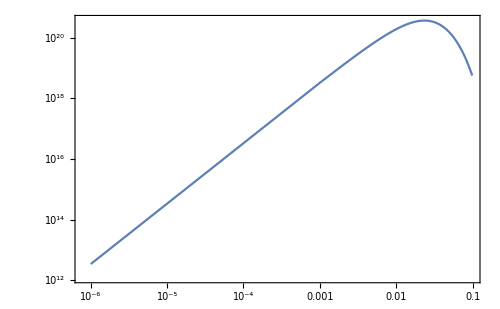

```mathematica
p0=ListLogLogPlot[Table[{x,ϕdet[10^15,0,x]},{x,10^-6,10^-1,0.001}],Joined->True,Frame->True,ImageSize->500]//Quiet
```

```mathematica
SetDirectory[NotebookDirectory[]];
greybodydata=Import["interpolation.dat","Table"];
```

```mathematica
func=Interpolation[greybodydata];
```

```mathematica
f[x_]:=func[x];
```

```mathematica
ϕdetinterpol[mpbh_?NumericQ,x_?NumericQ]:=1/(2*π)*(27*x^2*f[x])/(Exp[8*π*x]+1)*1.52*10^24; (*mpbh in g*) (*conversion from GeV to s^-1*)
```

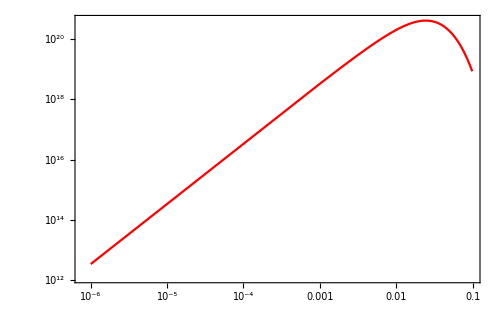

```mathematica
pin0=ListLogLogPlot[Table[{x/(G*10^15*5.62*10^23),ϕdetinterpol[10^15,x]},{x,G*10^15*5.62*10^23*10^-6,G*10^15*5.62*10^23*10^-1,G*10^16*5.62*10^23*0.0001}],Joined->True,Frame->True,PlotStyle->Red,ImageSize->500]//Quiet
```

```mathematica
data1=Import["instantaneous_primary_spectra15.txt","Table"];
```

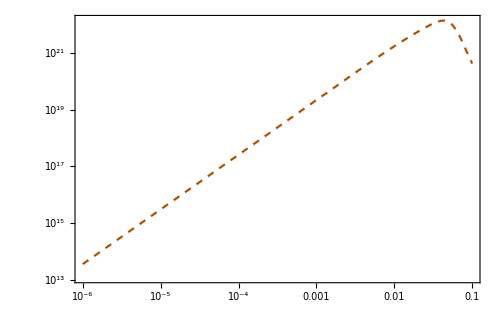

```mathematica
q0=ListLogLogPlot[Table[{data1[[i,1]],data1[[i,7]]},{i,Length[data1]}],PlotRange->{{10^-6,10^-1},Automatic},PlotStyle->{Darker[Orange],Dashed},Frame->True,Joined->True,ImageSize->500]
```

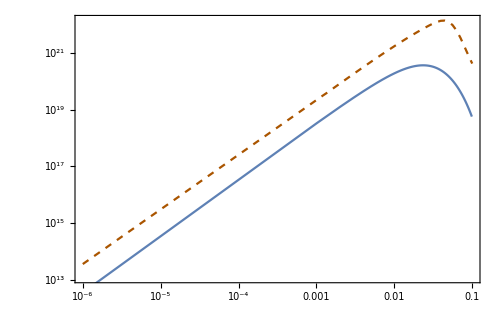

```mathematica
Show[q0,p0]
```